```mathematica
Tau=2Pi;
Second[lst_]:=lst[[2]];
Middle[xs_]:=xs[[Floor[(Length[xs]+1)/2]]];
WithXRegion[a_,b_][xs_]:=Block[{n=Length[xs]},Table[{a + (b-a) i/n, xs[[i]]},{i,1,n}]];
SimpsonSum[xs_]:=Block[{n=Length[xs]},
xs[[1]] + 4Sum[xs[[j]], {j, 2, n-1, 2}] + 2Sum[xs[[j]],{j,3,n-1,2}]+xs[[n]]
];

M[a_, L_, w_, resolution_:0] := Module[{n,x,da,coefficient, E},
n =If[resolution≠ 0,resolution, Max[30, 10 L / a // Ceiling]];
If[w == 0, Return[0.5 IdentityMatrix[2n]]];

x[i_]:=L (i-1/2)/n;
da[dx_]:=Sqrt[a^2 + dx^2];

coefficient[α_,β_][i_,j_]:=If[α==β,0,-a w/Tau BesselK[1, w da[x[i]-x[j]]] / da[x[i] - x[j]]]//N;
E = Table[Table[coefficient[α,β][i,j],{i,1,n},{j,1,n}],{α,0,1},{β,0,1}]//ArrayFlatten;
E + 0.5IdentityMatrix[2n]
];

v[a_,L_,w_,resolution_:0]:=Module[{n,x,da,K0,K1,V,source},
n =If[resolution≠0,resolution,Max[30, 10 L / a // Ceiling]];
If[w == 0, Return[Table[0, {i, 1, n}, {j, 1, n}]]];

x[i_]:=L(i-1/2)/n;
da[dx_]:=Sqrt[a^2 + dx^2];
K0=BesselK[0,#]&; K1=BesselK[1,#]&;

source[α_,β_][i_,j_]:= If[α==β,0,
-1/Tau K0[w da[x[i]-x[j]]]
-L w a/Tau^2NIntegrate[ K1[w da[x[i]-L t]]/da[x[i]-L t] *  K0[w Abs[x[j]-L t]],{t,0,1}]
]//Re;
V=ParallelTable[source[0,1][i,j],{i,1,n},{j,1,n}];
ArrayFlatten[{{ConstantArray[0,{Length[V],Length[V[[1]]]}], V},{V,ConstantArray[0,{Length[V],Length[V[[1]]]}]}}]
];
test[a_,L_,w_,resolution_:0]:=Module[{coefficients,source,p, diagonal},
coefficients = M[a,L,w,resolution];
ListPlot3D[coefficients]//Print;
ListPlot3D[coefficients,PlotRange->{0,All}]//Print;
ListPlot3D[coefficients,PlotRange->{All,0}]//Print;
source = v[a,L,w,resolution];
ListPlot3D[source]//Print;
p = LinearSolve[coefficients, source];
ListPlot3D[p]//Print;
diagonal=Table[p[[k,k]],{k,1,Length[p]/2}];
Middle[diagonal]//Print;
ListLinePlot[diagonal//WithXRegion[0,L]]//Print;
ListLinePlot[Table[diagonal[[k]],{k,2Length[diagonal]/5,3 Length[diagonal]/5}]//WithXRegion[2L/5,3L/5],PlotRange->{All,0}]//Print;
ListPlot3D[Table[p[[i,j]],{i,1,Length[p]/2},{j,1,Length[p]/2}]]//Print;
];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

0.173994

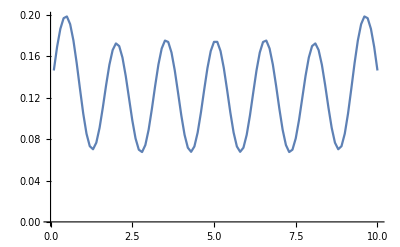

-Graphics-

-Graphics3D-

```mathematica
test[1,10,1]
```

```mathematica
ListPlot3D[cxs]
```

-Graphics3D-

```mathematica
ListPlot3D[src]
```

-Graphics3D-